## Getting the dielectric constant ϵ in a truly 2D layer with 1D wires in it

Marco Gibertini and Giovanni Pizzi

May 12th, 2015

We start from the formulas discussed in P. Cudazzo et al., PRB 84, 085406 (2011). There, they get the form of ϵ(q) and of the potential felt by an electron in the 2D dielectric in the presence of a point charge at distance ρ=(x,y) in the plane, Eq. (7).

I first check that Mathematica can understand 2D Fourier transforms properly, I transform here 1/q:

```mathematica
FourierTransform[1/(√(qx^2+qy^2)),{qx,qy},{rx,ry}]
```

1/(√(rx^2+ry^2))

I also transform 1/(|q|^2):

```mathematica
myf[rx_,ry_]:=FourierTransform[1/(qx^2+qy^2),{qx,qy},{rx,ry}]
```

```mathematica
myf[rx,ry]
```

1/2 (-HeavisideTheta[-rx] (2 EulerGamma+2 Log[-rx]+Log[1+ry^2/rx^2])-HeavisideTheta[rx] (2 EulerGamma+2 Log[rx]+Log[1+ry^2/rx^2]))

Here it is less obvious that the result is the excepted one, but if I call r=√(rx^2+ry^2), I can reduce the formula to:

```mathematica
EulerGamma+Log[r]
```

Let's now try to transform Eq. (5) of the paper mentioned above. Unfortunately, like this Mathematica cannot do it.

```mathematica
FourierTransform[1/(√(qx^2+qy^2)(1+√(qx^2+qy^2))),{qx,qy},{rx,ry}]
```

FourierTransform[1/(√(qx^2+qy^2) (1+√(qx^2+qy^2))),{qx,qy},{rx,ry}]

If we consider a system that is homogeneous along y, so that we can integrate this variable out (in order to consider the interaction with a wire of charge) and derivatives w.r.t. y can be discarded, we can simply replace √(qx^2+qy^2)  with |q_x|. If there was no absolute value, Mathematica can integrate it, but this is not what we want:

```mathematica
tr[rx_]:=FourierTransform[1/(qx(1+qx)),qx,rx]
```

```mathematica
tr[rx]
```

ⅈ ⅇ^(-ⅈ rx) (-1+ⅇ^(ⅈ rx)) √(π/2) Sign[rx]

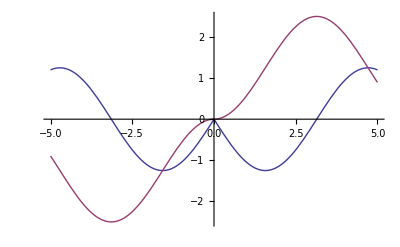

```mathematica
Plot[{Re[tr[rx]],Im[tr[rx]]}, {rx,-5,5}]
```

Asking Mathematica to Fourier transform the function with absolute value is tricky. However, we can write 1/(|q|(1+|q|))=1/(|q|)-1/(1+|q|), so we can try to transform the two pieces independently. The first part is easy:

```mathematica
FourierTransform[1/Abs[qx],qx,rx]
```

(-2 EulerGamma-2 Log[Abs[rx]])/(√(2 π))

The second part is a bit more tricky, but still possible. We will also consider only rx>0 and then use parity for rx<0:

```mathematica
FourierTransform[1/(Abs[qx]+1),qx,rx]
```

```mathematica
FullSimplify[1/(2 √(2 π) Abs[rx])ⅇ^(-ⅈ rx) (ⅈ π rx-Abs[rx] (2 CosIntegral[rx]+2 ⅇ^(2 ⅈ rx) ExpIntegralEi[-ⅈ rx]-ⅇ^(2 ⅈ rx) Log[-ⅈ rx]+ⅇ^(2 ⅈ rx) Log[ⅈ rx]-2 Log[rx]+2 Log[Abs[rx]]+ⅈ ⅇ^(2 ⅈ rx) π Sign[rx]+2 ⅈ SinIntegral[rx])), Assumptions->{rx∈Reals}]
```

Piecewise[{{Indeterminate, rx==0}, {(-2 Cos[rx] CosIntegral[rx]+Sin[rx] (π-2 SinIntegral[rx]))/(√(2 π)), rx>0}, {(ⅈ ⅇ^(-ⅈ rx) (π+2 ⅈ CosIntegral[rx]+2 ⅇ^(2 ⅈ rx) (π+ⅈ ExpIntegralEi[-ⅈ rx])-2 SinIntegral[rx]))/(2 √(2 π)), True}}]

```mathematica
FullSimplify[(-2 EulerGamma-2 Log[Abs[rx]])/(√(2 π))-(-2 Cos[rx] CosIntegral[rx]+Sin[rx] (π-2 SinIntegral[rx]))/(√(2 π)),Assumptions->{rx>0}]
```

1/(√(2 π))(2 Cos[rx] CosIntegral[rx]-2 (EulerGamma+Log[rx])-π Sin[rx]+2 Sin[rx] SinIntegral[rx])

This is the result for this second contribution, using CosIntegral and SinIntegral functions:

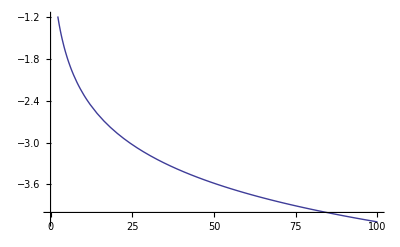

```mathematica
Plot[1/(√(2 π))(2 Cos[rx] CosIntegral[rx]-2 (EulerGamma+Log[rx])-π Sin[rx]+2 Sin[rx] SinIntegral[rx]), {rx, 0, 100}]
```

The quantity we have obtained in this way should simply be the potential energy felt by an electron in the presence of a charge wire, that we can obtain integrating Eq. (7) on y, we do it numerically:

```mathematica
Inte[rx_]:=NIntegrate[StruveH[0,√(rx^2+ry^2)]-BesselY[0,√(rx^2+ry^2)],{ry,-∞,∞}]
```

```mathematica
MyIntTable = Table[{i,Inte[i]},{i,-10,10}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ry near {ry} = {4.81037×10^7}. NIntegrate obtained 15.4968 and 2.41266 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ry near {ry} = {4.81037×10^7}. NIntegrate obtained 15.6282 and 2.41278 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ry near {ry} = {4.81037×10^7}. NIntegrate obtained 15.7745 and 2.41287 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

{{-10,15.4968},{-9,15.6282},{-8,15.7745},{-7,15.9393},{-6,16.128},{-5,16.3481+5.89559×10^-21 ⅈ},{-4,16.6121-3.9304×10^-21 ⅈ},{-3,16.9408-5.89559×10^-21 ⅈ},{-2,17.3739-3.9304×10^-21 ⅈ},{-1,18.0033+9.13904×10^-29 ⅈ},{0,19.1734-3.9304×10^-21 ⅈ},{1,18.0033+9.13904×10^-29 ⅈ},{2,17.3739-3.9304×10^-21 ⅈ},{3,16.9408-5.89559×10^-21 ⅈ},{4,16.6121-3.9304×10^-21 ⅈ},{5,16.3481+5.89559×10^-21 ⅈ},{6,16.128},{7,15.9393},{8,15.7745},{9,15.6282},{10,15.4968}}

I remove an offset (an integration constant), that is the value for rx = 0

```mathematica
MyIntTable2 = Table[{MyIntTable[[x,1]],MyIntTable[[x,2]]-19.17338092988501}, {x,1,Length[MyIntTable]}]
```

{{-10,-3.67661},{-9,-3.54516},{-8,-3.39888},{-7,-3.23405},{-6,-3.04543},{-5,-2.82525+5.89559×10^-21 ⅈ},{-4,-2.56124-3.9304×10^-21 ⅈ},{-3,-2.23258-5.89559×10^-21 ⅈ},{-2,-1.79949-3.9304×10^-21 ⅈ},{-1,-1.17012+9.13904×10^-29 ⅈ},{0,0.-3.9304×10^-21 ⅈ},{1,-1.17012+9.13904×10^-29 ⅈ},{2,-1.79949-3.9304×10^-21 ⅈ},{3,-2.23258-5.89559×10^-21 ⅈ},{4,-2.56124-3.9304×10^-21 ⅈ},{5,-2.82525+5.89559×10^-21 ⅈ},{6,-3.04543},{7,-3.23405},{8,-3.39888},{9,-3.54516},{10,-3.67661}}

And now I plot it: we have to take into account that we have used from the beginning, when using Eq. (5), 2πα=r_0=1, so the proper factors should be considered. Moreover, probably the FT in Mathematica has a different prefactor. Comparing the numerical integral of Eq. (7) with the solution obtained above, we get a good comparison (the difference at large rx is most probably due to numerical errors in the integral from -∞ to ∞, as also indicated by the various warnings).

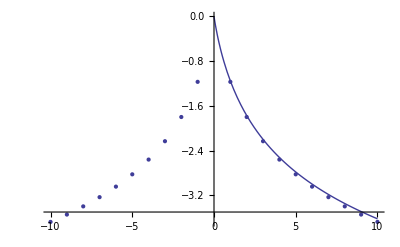

```mathematica
Show[ListPlot[MyIntTable2],Plot[π/2*1/(√(2 π))(2 Cos[rx] CosIntegral[rx]-2 (EulerGamma+Log[rx])-π Sin[rx]+2 Sin[rx] SinIntegral[rx]), {rx, 0, 10}],PlotRange->All]
```

We can also check a larger interval, from -100 to 100:

```mathematica
MyIntTable3 = Table[{i,Inte[i]},{i,-100,100,10}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ry near {ry} = {4.81037×10^7}. NIntegrate obtained 12.5826  - 5.89558×10^-21\ ⅈ
 and 2.41331 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ry near {ry} = {4.81037×10^7}. NIntegrate obtained 12.7272 and 2.42206 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ry near {ry} = {4.81037×10^7}. NIntegrate obtained 12.871 and 2.42577 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

{{-100,12.5826-5.89558×10^-21 ⅈ},{-90,12.7272},{-80,12.871},{-70,13.0217-9.15343×10^-29 ⅈ},{-60,13.2224+5.89559×10^-21 ⅈ},{-50,13.4449},{-40,13.7489},{-30,14.1109+3.93039×10^-21 ⅈ},{-20,14.6249},{-10,15.4968},{0,19.1734-3.9304×10^-21 ⅈ},{10,15.4968},{20,14.6249},{30,14.1109+3.93039×10^-21 ⅈ},{40,13.7489},{50,13.4449},{60,13.2224+5.89559×10^-21 ⅈ},{70,13.0217-9.15343×10^-29 ⅈ},{80,12.871},{90,12.7272},{100,12.5826-5.89558×10^-21 ⅈ}}

Also here I remove the offset:

```mathematica
MyIntTable4 = Table[{MyIntTable3[[x,1]],MyIntTable3[[x,2]]-19.17338092988501}, {x,1,Length[MyIntTable3]}]
```

{{-100,-6.59074-5.89558×10^-21 ⅈ},{-90,-6.44616},{-80,-6.30235},{-70,-6.15169-9.15343×10^-29 ⅈ},{-60,-5.95101+5.89559×10^-21 ⅈ},{-50,-5.72853},{-40,-5.42452},{-30,-5.06249+3.93039×10^-21 ⅈ},{-20,-4.54852},{-10,-3.67661},{0,-3.00204×10^-12-3.9304×10^-21 ⅈ},{10,-3.67661},{20,-4.54852},{30,-5.06249+3.93039×10^-21 ⅈ},{40,-5.42452},{50,-5.72853},{60,-5.95101+5.89559×10^-21 ⅈ},{70,-6.15169-9.15343×10^-29 ⅈ},{80,-6.30235},{90,-6.44616},{100,-6.59074-5.89558×10^-21 ⅈ}}

And I show it in the new range :

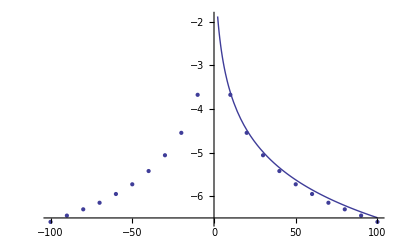

```mathematica
Show[ListPlot[MyIntTable4],Plot[π/2*1/(√(2 π))(2 Cos[rx] CosIntegral[rx]-2 (EulerGamma+Log[rx])-π Sin[rx]+2 Sin[rx] SinIntegral[rx]), {rx, 0, 100}],PlotRange->All]
```

So, the formula that we obtained allows to write directly V_eff(x) where x is the distance from the 1D wire, and could be used in a Schroedinger-Poisson code. If one wants to consider a periodic array of wires, one can discretize the charge density on a grid, perform a FFT, and then multiply by the correct coefficients that can be obtained from Eq. (5) directly at the correct G points in q_x space, without the need of the expression above. However, the difficulty in a real case is that here we are assuming a constant α for the whole plane. Instead, typically we have at least two different “stripes” with different α (e.g., BN and functionalized BN). In this case, however, since α=α(x), we cannot treat it as a constant, and so already in Eq. (2) we don’t have α∇^2 ϕ but ∇α(x)∇ϕ(x), and in Fourier Transform when going to Eq. (4), we cannot simply multiply by α but we will have a convolution of α and ϕ, making the results much more complex. Another possibility would be to use the expression that we have obtained at the top of this Mathematica file for each stripe, and then use the correct boundary conditions (BC) at each interface. In 1D however one has to be careful to understand which is the correct BC to apply. For comparison, in 3D with 2D interfaces, the equation can be written as

∇ϵ∇V=-n(x)=∇ϵ∇V+ϵ∇^2 V=-n(x)

For each interval we will have two free parameters when solving the differential equation ϵ∇^2 V=-n(x); at each interface, we have the continuity of V as one condition, and the condition ϵ_1 V_1-ϵ_2 V_2=0 for the continuity of the orthogonal component of D, that originates by the term ∇ϵ∇V and can be obtained by integrating in a small cylinder around the interface. If we have N materials, we will have thus 2N free parameters, 2(N-1) constraints from the interfaces, and finally: 1 parameter to impose the global electric field, and 1 free parameter (an additive constant to V that has no physical meaning). 
In 1D, the continuity of V is still a valid condition, as well as the global electric field; one has however to understand how to rewrite the condition for the continuity of D: in fact, the equation from which one starts (obtained similarly to the paper, but then integrating over y) is

-∇^2 ϕ(x,z)=n(x)δ(z)+∇(α∇ϕ(x,z=0))δ(z)